```mathematica
LoadPXD[name_, {rhon_,rn_,ln_,pn_}]:=Module[{data=Import[FileNameJoin[{NotebookDirectory[],name}]],lambdas,rs,rhos,pxd},
rs=First[data[[rn]]];rhos=First[data[[rhon]]];lambdas=First[data[[ln]]];pxd=data[[pn]];ListInterpolation[pxd,{lambdas,rs,rhos}]]
```

```mathematica
AbcCombined = LoadPXD["ABC/oes_eyp_bs_combined_atra_control_cond_prior.mat",{3,2,1,4}];
{{λmin,λmax},{rmin,rmax},{ρmin,ρmax}}=AbcCombined[[1]];
```

```mathematica
ρticks=Table[ρ,{ρ,0,1,0.2}];
rticks=Table[r,{r,0,0.5,0.1}];
λticks=Table[λ,{λ,λmin,λmax,0.1}];
```

```mathematica
blobplot=ContourPlot3D[AbcCombined[λ,r,ρ],{ρ,ρmin,ρmax},{r,rmin,rmax},{λ,λmin,λmax},Contours->{129.4380,1087.9},ContourStyle->Directive[Orange,Opacity[0.4],Specularity[White,30]],Mesh->False,ViewPoint->{π/2,-π,2},FaceGrids->{{{-1,0,0},{rticks,λticks}},{{0,1,0},{ρticks,λticks}},{{0,0,-1},{ρticks,rticks}}},Boxed->False,Axes->True,AxesLabel->{ρ,r,λ},BoundaryStyle->None];
```

```mathematica
Show[blobplot, PlotRange->{{0,1},{0,0.5},{λmin,λmax}}]/.Graphics3D[gr_,opts_]:>Graphics3D[{gr,(Scale[gr,#1,{0,0.5,λmin}]&)/@(1+1/10^3-IdentityMatrix[3])},opts]
Export[FileNameJoin[{NotebookDirectory[],"ABC/oes_eyp_bs_combined_atra_control_cond_prior.png"}],Image[%,ImageResolution->300]];
```

-Graphics3D-

```mathematica
AbCombined = LoadPXD["AB/oes-eyp-b-combined-prior.mat",{3,4,1,2}];
```

```mathematica
sheetplot=RegionPlot3D[AbCombined[λ,r,ρ]>15.0462,{ρ,0,1},{r,0,0.5},{λ,λmin,λmax},PlotPoints->40,PlotStyle->Directive[LightBlue,Opacity[0.5],Specularity[White,30]],Mesh->False,ViewPoint->{-π,-π/2,2},FaceGrids->{{{1,0,0},{rticks,λticks}},{{0,1,0},{ρticks,λticks}},{{0,0,-1},{ρticks,rticks}}},Boxed->False,Axes->True,AxesLabel->{ρ,r,λ}];
```

InterpolatingFunction::dmval: Input value {0.6`, 0.`, 0.`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.6102564102564102`, 0.`, 0.`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

```mathematica
Intersect = LoadPXD["oes-combined-prior.mat",{1,2,3,4}];
```

```mathematica
intersectplot=ContourPlot3D[Intersect[λ,r,ρ],{ρ,ρmin,ρmax},{r,rmin,rmax},{λ,λmin,λmax},Contours->{351.1307, 3.0759*^3},ContourStyle->Directive[Green,Opacity[0.4],Specularity[White,30]],Mesh->False,ViewPoint->{π/2,-π,2},FaceGrids->{{-1,0,0},{0,1,0},{0,0,-1}},Boxed->False,Axes->True,AxesLabel->{ρ,r,λ},BoundaryStyle->None];
```

```mathematica
Show[sheetplot,blobplot/.Graphics3D[gr_,opts_]:>Graphics3D[{gr,(Scale[gr,#1,{1,0.5,λmin}]&)/@(1+1/10^3-IdentityMatrix[3])},opts],intersectplot/.Graphics3D[gr_,opts_]:>Graphics3D[{gr,(Scale[gr,#1,{1,0.5,λmin}]&)/@(1+1/10^3-IdentityMatrix[3])},opts]]
```

-Graphics3D-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"oes-combined-prior.png"}],Image[%,ImageResolution->300]];
```

Out::intm: Machine-size integer expected at position 1 in Out[0.`].

Image::imgarray: The specified argument Out[0] should be an array of rank 2 or 3 with machine-size numbers.

Out::intm: Machine-size integer expected at position 1 in Out[0.`].

Image::imgarray: The specified argument Out[0] should be an array of rank 2 or 3 with machine-size numbers.

```mathematica
p[λ_,ρ_,Λ_,t_]:=ρ Exp[-Λ t] + (1-ρ) Exp[-λ t]
likelihood[p_,m_,M_]:=Binomial[M,m] p^m (1-p)^(M-m)
```

```mathematica
singleclonedata={{3/7, 21+20+28, 38+50+52},{3,13+25+16,300},{6,2+6+4,67+96+90},{12,5+5+1,172+131+83},{26,2+0+3,115+111+116},{52,2,214}};
```

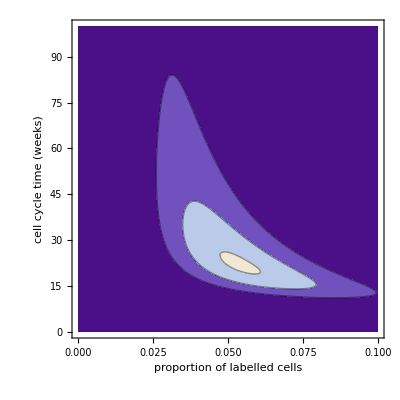

```mathematica
ContourPlot[Exp[Plus@@Log[(likelihood[p[0.7676,ρ,1/τ,#1⟦1⟧],#1⟦2⟧,#1⟦3⟧]&)/@singleclonedata]-Log[τ]+30],{ρ,0,0.1},{τ,0,100},WorkingPrecision->∞,FrameLabel->{"proportion of labelled cells","cell cycle time (weeks)"},MaxRecursion->5,WorkingPrecision->40,RotateLabel->True,PlotRange->{0,1.7*^-16*Exp[30]},Contours->{1-0.95,1-0.68,0.9} 1.70*^-16*Exp[30]]
Export[FileNameJoin[{NotebookDirectory[],"single-cell-inference.png"}],Image[%,ImageResolution->300]];
```

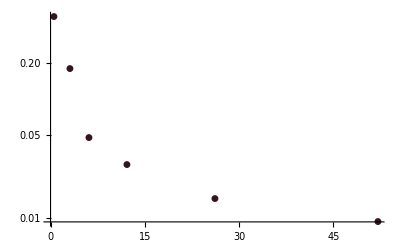

```mathematica
singleclonedataplot=ListLogPlot[{#[[1]], #[[2]]/#[[3]]}& /@ singleclonedata,PlotMarkers->Automatic,PlotStyle->ColorData[21,"ColorList"]]
```

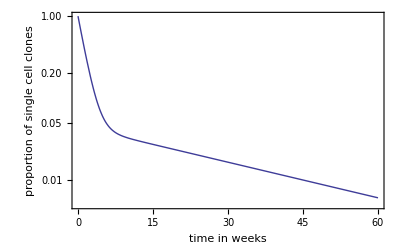

```mathematica
singleclonetheoryplot=LogPlot[p[0.7676,0.045032,0.033299,t],{t,0,60},FrameLabel->{Text["time in weeks"],"proportion of single cell clones"},PlotRange->{0.005,1},RotateLabel->True,Frame->True]
```

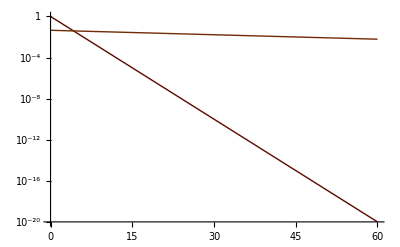

```mathematica
singlecellcptheoryplot=LogPlot[{p[0.7676,0,0.033299,t],0.045032 Exp[-0.033299 t]},{t,0,60},PlotStyle->ColorData[23,"ColorList"]]
```

```mathematica
Needs["ErrorBarPlots`"]
Needs["ErrorBarLogPlots`",FileNameJoin[{NotebookDirectory[],"ErrorBarLogPlots.m"}]]
```

```mathematica
singleclonetheoryerror[n_]:=ErrorListLogPlot[({{t,p[λ,ρ,Λ,t]},ErrorBar[n √((p[λ,ρ,Λ,t] (1-p[λ,ρ,Λ,t]))/(#1⟦3⟧))]}/.t->#1⟦1⟧&)/@singleclonedata/.{λ->0.7676,ρ->0.045032,Λ->0.033299},PlotMarkers->Graphics[],ErrorBarFunction->Function[{coords, errs}, {Opacity[0.3],Rectangle[coords+{-0.5,errs⟦2,1⟧},coords+{0.5,errs⟦2,2⟧}]}]]
```

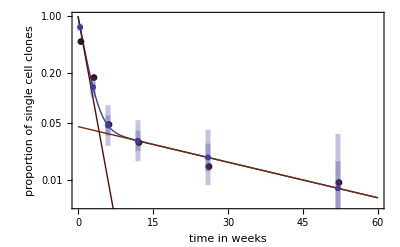

```mathematica
Show[singleclonetheoryplot,singlecellcptheoryplot,singleclonedataplot,singleclonetheoryerror[1],singleclonetheoryerror[2]]
Export[FileNameJoin[{NotebookDirectory[],"single-cell-clones.png"}],Image[%,ImageResolution->300]];
```